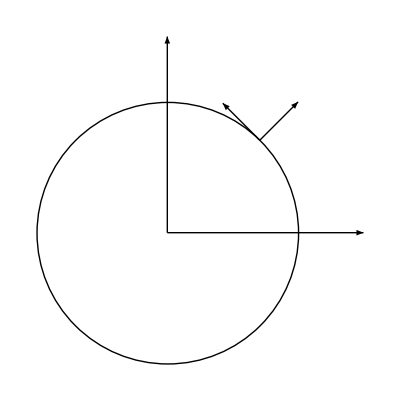

```mathematica
Show[Graphics[Arrow[{{0,0},{0,1.5}}]],Graphics[Arrow[{{0,0},{1.5,0}}]],Graphics[Arrow[{{Cos[π/4],Sin[π/4]},{1,1}}]],Graphics[Circle[]],Graphics[Arrow[{{Cos[π/4],Sin[π/4]},{Cos[π/4]-0.4Sin[π/4],Sin[π/4]+0.4Cos[π/4]}}]]]
```

```mathematica
θ=π/4
ϕ=π/4
```

π/4

π/4

```mathematica
plt=Show[Graphics3D[{Opacity[0.2],Sphere[]}],Graphics3D[{Green,Arrow[{{0,0,0},{1.5,0,0}}]}],Graphics3D[{Green,Arrow[{{0,0,0},{0,1.5,0}}]}],Graphics3D[{Green,Arrow[{{0,0,0},{0,0,2}}]}],Graphics3D[{Red,Arrow[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{Sin[θ]Cos[ϕ]-Cos[θ]Cos[ϕ],Sin[θ]Sin[ϕ]-Cos[θ]Sin[ϕ],Cos[θ]+Sin[θ]}}]}],Graphics3D[{Red,Arrow[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{2Sin[θ]Cos[ϕ],2Sin[θ]Sin[ϕ],2Cos[θ]}}]}],Graphics3D[{Red,Arrow[{{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{Sin[θ]Cos[ϕ]-Sin[ϕ],Sin[θ]Sin[ϕ]+Cos[ϕ],Cos[θ]}}]}],Graphics3D[{Blue,Arrow[{{0,0,0},{Cos[ϕ],Sin[ϕ],0}}]}],Graphics3D[{Blue,Arrow[{{0,0,0},{-Sin[ϕ],+Cos[ϕ],0}}]}],Graphics3D[Line[{{0,0,0},{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}}]],Graphics3D[{Yellow,Sphere[{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},0.1]}],Graphics3D[Text["(ê)_r",{2Sin[θ]Cos[ϕ]+0.05,2Sin[θ]Sin[ϕ]+0.05,2Cos[θ]+0.05}]],Graphics3D[Text["(ê)_ϕ",{Sin[θ]Cos[ϕ]-Sin[ϕ]-0.05,Sin[θ]Sin[ϕ]+Cos[ϕ]+0.05,Cos[θ]}]],Graphics3D[Text["(ê)_θ",{Sin[θ]Cos[ϕ]-Cos[θ]Cos[ϕ]-0.07,Sin[θ]Sin[ϕ]-Cos[θ]Sin[ϕ]-0.07,Cos[θ]+Sin[θ]-0.05}]],Graphics3D[Text["o⃗",{Cos[ϕ]+0.03,Sin[ϕ]+0.03,-0.05}]],
Graphics3D[Text["s⃗",{-Sin[ϕ]-0.03,+Cos[ϕ]+0.03,-0.05}]],
Graphics3D[Text["x",{1.6,0,0}]],
Graphics3D[Text["y",{0,1.6,0}]],
Graphics3D[Text["z",{0,0,2.1}]]]
```

-Graphics3D-

```mathematica
Append[plt,Boxed->False]
```

-Graphics3D-

```mathematica
Sin[θ]Cos[ϕ]
```

1/2